```mathematica
Clear["Global`*"]
```

### 関数過去

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる:ランク) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex[PartLoop]}];
EdgeRules[Gout][[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
NewDirectedGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築 *)
EdgeProcess={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
For[j=1,
Length[PartLoopVertexProcess]≠ Length[Pin],
j++,
If[!SubsetQ[PartLoopVertexProcess,VertexList[{EdgeRules[Gout][[SortList[[j]]]]}]],
EdgeProcess=Append[EdgeProcess,EdgeRules[Gout][[SortList[[j]]]]]
];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]]];
];
PartLoopProcess
)
```

```mathematica
DelEdgeNumOfRestPartLoop[EdgeListNum_,PartLoop_]:=DelEleList[EdgeListNum,DelEleList[EdgeNumListVertex[Subsets[VertexList[PartLoop],{2}]],EdgeNumList[PartLoop]]](* PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を枝リストの枝番号から削除する *)
```

```mathematica
NewDirectedGreedyFromSort2[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築2(枝を追加してから余分な枝を削除するアルゴリズム) *)
EdgeProcessNum={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
DelEdgeProcess={};
For[j=1,Length[PartLoopVertexProcess]< Length[Pin],j++,
EdgeProcessNum=Append[EdgeProcessNum,SortList[[j]]];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]];
DelEdge={};
For[k=1,k≤Length[PartLoopProcess],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,EdgeRules[PartLoopProcess[[k]]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
DelEdgeProcess=Append[DelEdgeProcess,DelEdge];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]]
];
PartLoopProcess
)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
PluralPartLoopByGreedyFromRank[Rank_]:=(
PartLoopProcess={};
For[i=3,Length[PartLoopProcess]==0,i++,
PartLoopProcess=FindCycle[
Graph[EdgeList[Gout][[Rank[[Range[i]]]]]],
Infinity,All]
];
EdgeRulesList[PartLoopProcess]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築 *)
```

```mathematica
DelEdgePluralPartLoop[PartLoopList_]:=(
EdgeProcessNum=EdgeNumList[Flatten[PartLoopList]];
DelEdge={};
For[k=1,k≤Length[PartLoopList],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,PartLoopList[[k]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
EdgeRulesList[FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]
)
(* Delete Edge from Plural PartLoop, 複数の部分巡回路から、PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を削除し、再度、複数の部分巡回路を見つける *)
```

```mathematica
PluralPartLoopByGreedyFromRank2[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築2(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin={{3.6460755930247206,3.673313315610663},{5.825076999866807,1.75039279642003},{7.006163937920729,9.557741324132841},{0.029767020509346764,8.772618913921029},{6.464446665138183,0.8225074837016031},{1.3267938998486812,2.0322656366692033},{1.9441107440749956,9.59138461443171},{5.131917172513887,3.6983652708061303},{0.2707145244147746,1.1726209314243707},{2.2707158300231463,1.0374810126441947}}
(*Point input*)
```

{{3.64608,3.67331},{5.82508,1.75039},{7.00616,9.55774},{0.029767,8.77262},{6.46445,0.822507},{1.32679,2.03227},{1.94411,9.59138},{5.13192,3.69837},{0.270715,1.17262},{2.27072,1.03748}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

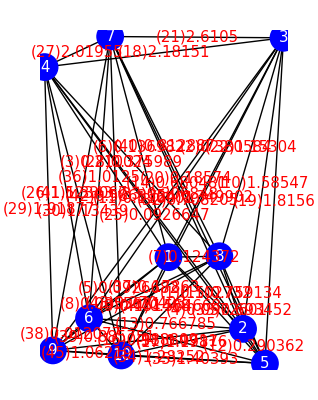

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{28.2885,17.8047,29.7655,70.01,30.6593,44.9544,11.9484,118.125,19.6362,4.98034,77.8844,3.8808,5.87793,12.8569,2.72366,5.64753,3.02408,3.21816,4.82045,50.7594,1.93916,5.33532,35.051,27.8586,110.375,4.50562,1.03096,19.1384,3.96286,7.09916,5.43524,13.9302,4.57072,4.83706,2.99106,7.49064,23.2542,112.754,1.54823,8.24221,6.4505,14.5994,20.2594,6.91959,1.88719}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{27,39,45,21,15,35,17,18,12,29,26,33,19,34,10,22,31,16,13,41,44,30,36,40,7,14,32,42,2,28,9,43,37,24,1,3,5,23,6,20,4,11,25,38,8}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{33.0305,{1,8,2,5,10,9,6,4,7,3,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法3

```mathematica
PluralPartLoopByGreedyFromRank[PDCurrCostSort]
```

{{4→9,9→10,10→5,5→3,3→4},{4→6,6→10,10→5,5→3,3→4},{7→4,4→9,9→10,10→5,5→3,3→7},{7→4,4→6,6→10,10→5,5→3,3→7}}

```mathematica
{PartLoop1,PartLoop2}=DelEdgePluralPartLoop[{{4->9,9->10,10->5,5->3,3->4},{4->6,6->10,10->5,5->3,3->4},{7->4,4->9,9->10,10->5,5->3,3->7},{7->4,4->6,6->10,10->5,5->3,3->7}}]
```

{{4→6,6→10,10→5,5→3,3→7,7→4},{4→9,9→10,10→5,5→3,3→7,7→4}}

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

{3,5,10,6,4,7,3}

-Graphics-

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[line=Line[Pin[[%]]]]
```

{3,5,10,9,4,7,3}

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
EdgeProcess=Intersection[PartLoop1,PartLoop2];
PartLoop12Order=Ordering[PDCurrCost[[EdgeNumList[PartLoop12 = ComplementIntersection[PartLoop1, PartLoop2]]]]];
PartLoopProcess={};
For[j=1,PartLoopProcess=={},j++,
EdgeProcess=Append[EdgeProcess,PartLoop12[[PartLoop12Order[[j]]]]];
PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]
]
PartLoop3=EdgeRulesList[PartLoopProcess][[1]]
```

{3→7,7→4,4→9,9→10,10→5,5→3}

{3,5,10,9,4,7,3}

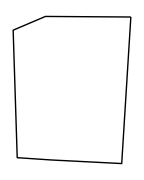

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
Graphics[line=Line[Pin[[%]]]]
```

#### 外側の頂点は一つだけの場合、追加コストが一番小さくなる所に挿入する

```mathematica
PartLoop3={3->7,7->4,4->6,6->10,10->5,5->3};
```

```mathematica
OutVertex1=OutVertex[PartLoop3][[1]]
```

9

```mathematica
MinTriTourDiffPosition[PartLoop3,OutVertex1]
```

4

```mathematica
TriTourDiffList[PartLoop3,OutVertex1]
```

{14.2766,14.1052,2.10153,1.99494,4.00894,8.20691}

```mathematica
PartLoop3[[4]]
```

6→10

```mathematica
Join[Delete[PartLoop3,4],{PartLoop3[[4,1]]->OutVertex1,OutVertex1-> PartLoop3[[4,2]]}]
```

{3→7,7→4,4→6,10→5,5→3,6→9,9→10}

```mathematica
InsertVertex[PartLoop3,OutVertex1]
```

{3→7,7→4,4→6,10→5,5→3,6→9,9→10}

{3,5,9,4,7,3}

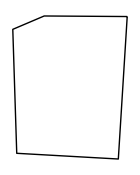

```mathematica
VertexSortFromLoopEdgeList[{3->7,7->4,4->6,10->5,5->3,4->9,9->5}]
Graphics[line=Line[Pin[[%]]]]
```

{3,5,10,9,6,4,7,3}

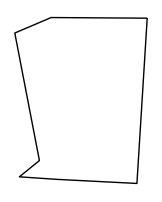

```mathematica
VertexSortFromLoopEdgeList[{7->4,4->6,10->5,5->3,3->7,6->9,9->10}]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],{3,5,10,9,6,4,7,3}]
```

{2→8,8→1,2→1}

{1,2,8,1}

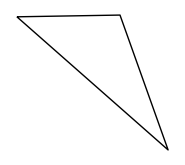

```mathematica
PartLoopByNewUndirectedGreedyFromSort[EdgeNumList[{2->8,8->1,2->1}]]
Graphics[line=Line[Pin[[%]]]]
```

### 一貫した新しいgreedyを用いた解法4

```mathematica
PluralPartLoopByGreedyFromRank2[PDCurrCostSort]
```

{7→4,4→9,9→10,10→5,5→3,3→7}

```mathematica
EdgeProcess
PartLoopProcess
DelEdge
AddEdge
```

{7→4,6→10,9→10,3→7,2→8,10→5,10→2,4→9}

{{7->4,4->9,9->10,10->5,5->3,3->7}}

{3→4,5→2,4→6,5→8}

5→3

{3,5,10,9,4,7,3}

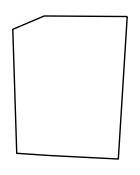

```mathematica
VertexSortFromLoopEdgeList[{7->4,4->9,9->10,10->5,5->3,3->7}]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],{3,5,10,9,4,7,3}]
```

{2→8,6→2,8→1,6→8,2→1,1→6}

{1,6,8,1}

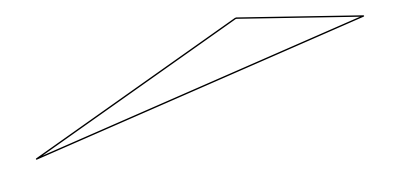

```mathematica
PartLoopByNewDirectedGreedyFromSort[EdgeNumList[{2->8,6->2,8->1,6->8,2->1,1->6}]]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
EdgeSolution
```

{8→1,1→6,6→8}

```mathematica
OutLoop3=JoinPartLoop[{7->4,4->9,9->10,10->5,5->3,3->7},{8->1,1->6,6->8}]
```

{7→4,4→9,9→10,5→3,3→7,8→1,1→6,10→6,5→8}

{1,6,10,9,4,7,3,5,8,1}

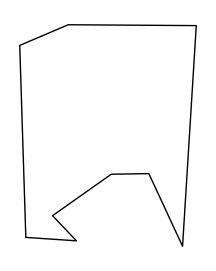

```mathematica
VertexSortFromLoopEdgeList[OutLoop3]
Graphics[Line[Pin[[%]]]]
```

```mathematica
OutLoop4=ContinuousInsertVertexLoop[OutLoop3]
```

{{7→4,4→9,9→10,5→3,3→7,8→1,1→6,10→6,5→8},{7→4,4→9,9→10,5→3,3→7,8→1,1→6,10→6,5→2,2→8}}

{1,6,10,9,4,7,3,5,2,8,1}

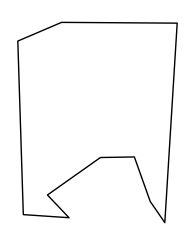

```mathematica
VertexSortFromLoopEdgeList[OutLoop4[[-1]]]
Graphics[Line[Pin[[%]]]]
```

```mathematica
ArcLength[Line[Pin[[{1,8,2,5,10,9,6,4,7,3,1}]]]]//N
```

33.0305

```mathematica
ArcLength[Line[Pin[[{1,6,10,9,4,7,3,5,2,8,1}]]]]//N
```

34.3977

### 重み付け

```mathematica
PDWeight=PD*Table[1+i*0.1,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{5.52167,25.7495,22.5052,9.62107,5.11406,20.937,2.08047,11.3421,5.94617,34.7432,45.524,1.23952,12.6199,41.9947,3.3082,17.8699,7.97533,28.0817,42.8849,48.083,14.6803,20.3011,59.1542,50.6885,55.2305,26.7696,3.53955,29.5029,32.6964,36.2395,15.8345,52.2868,6.6561,21.7127,10.918,31.854,10.3847,1.63407,1.78275,24.7899,40.3423,39.3766,16.9824,8.98673,3.00684}

```mathematica
PDWeightCurrRank=Ordering[Abs[PDWeight/Curr]]
```

{27,39,45,12,15,21,17,35,33,18,44,31,13,7,34,29,26,22,16,10,19,41,40,36,30,9,1,5,37,14,43,42,2,32,28,3,38,24,6,4,23,20,8,11,25}

```mathematica
Abs[PDWeight/Curr][[26]]
```

17.5719

```mathematica
Abs[PDWeight/Curr][[29]]
```

17.0403

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{27,39,45,21,15,35,17,18,12,29,26,33,19,34,10,22,31,16,13,41,44,30,36,40,7,14,32,42,2,28,9,43,37,24,1,3,5,23,6,20,4,11,25,38,8}

```mathematica
OutLoop1=PluralPartLoopByGreedyFromRank2[PDWeightCurrRank]
```

{7→4,4→9,9→10,10→2,2→8,8→3,3→7}

```mathematica
VertexSortFromLoopEdgeList[OutLoop1]
Graphics[Line[Pin[[%]]]]
```

{2,10,9,4,7,3,8,2}

-Graphics-

```mathematica
OutVertex[OutLoop1]
```

{5}

#### 内部の点から挿入する

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDWeightCurrRank]],Join[{2,10,9,4,7,3,8,2},OutVertex[OutLoop1]]]
```

{1→6}

```mathematica
PartLoop2=InsertEdge[OutLoop1,1->6]
```

{7→4,9→10,10→2,2→8,8→3,3→7,1→6,4→1,9→6}

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[Line[Pin[[%]]]]
```

{1,4,7,3,8,2,10,9,6,1}

-Graphics-

```mathematica
PartLoop3=InsertVertex[PartLoop2,5]
```

{7→4,9→10,2→8,8→3,3→7,1→6,4→1,9→6,10→5,5→2}

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
Graphics[Line1=Line[Pin[[%]]]]
```

{1,4,7,3,8,2,5,10,9,6,1}

-Graphics-

```mathematica
ArcLength[Line1]//N
```

33.1487

```mathematica
ArcLength[Line[Pin[[{1,8,2,5,10,9,6,4,7,3,1}]]]]//N
```

33.0305

### 重み付け(ウェイトをきつくする)

```mathematica
PDWeight2=PD*Table[1+i*5,{i,Length[PD]}][[Ordering[Ordering[PD]]]]
```

{133.683,955.442,818.94,284.623,116.487,745.111,31.2071,361.267,151.627,1350.25,1830.06,6.76103,410.147,1671.04,64.0963,619.861,221.134,1060.09,1715.39,1942.18,485.968,713.613,2430.7,2056.78,2260.36,1002.15,74.9552,1122.55,1262.23,1417.37,533.094,2130.93,177.496,781.656,340.138,1221.07,315.696,14.979,21.9415,911.198,1596.52,1549.38,580.689,257.88,52.1186}

```mathematica
PDWeightCurrRank2=Ordering[Abs[PDWeight2/Curr]]
```

{12,39,27,45,15,17,21,35,7,33,44,18,13,31,34,22,16,26,29,10,19,9,40,41,36,38,30,5,1,37,43,14,2,42,28,32,3,4,6,24,23,8,20,11,25}

```mathematica
OutLoop1=PluralPartLoopByGreedyFromRank2[PDWeightCurrRank2]
```

{2→8,8→3,3→7,7→4,4→6,6→10,10→2}

```mathematica
VertexSortFromLoopEdgeList[OutLoop1]
Graphics[Line[Pin[[%]]]]
```

{2,10,6,4,7,3,8,2}

-Graphics-

```mathematica
OutVertex[OutLoop1]
```

{5,9}

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDWeightCurrRank]],Join[{2,10,6,4,7,3,8,2},OutVertex[OutLoop1]]]
```

{}

```mathematica
DelEleList[Range[10],Join[{2,10,6,4,7,3,8,2},OutVertex[OutLoop1]]]
```

{1}

```mathematica
PartLoop2=InsertVertex[OutLoop1,1]
```

{2→8,3→7,7→4,4→6,6→10,10→2,8→1,1→3}

```mathematica
PartLoop2={2->8,3->7,7->4,4->6,6->10,10->2,8->1,1->3}
```

{2→8,3→7,7→4,4→6,6→10,10→2,8→1,1→3}

{1,8,2,10,6,4,7,3,1}

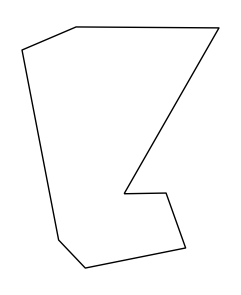

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[Line[Pin[[%]]]]
```

#### 最初にできたPartLoopの中で最もランクが低い枝よりもランクが高い、PartLoopの点を含まない枝を挿入する（挿入する枝をPartLoopとクロスしないと予想する）

```mathematica
Join[EdgeNumList[OutLoop1],EdgeNumListVertex[Subsets[OutVertex[OutLoop1],{2}]]]
```

{15,22,21,27,26,39,17,34}

```mathematica
SortSameAs[PDWeightCurrRank2,Join[EdgeNumList[OutLoop1],EdgeNumListVertex[Subsets[OutVertex[OutLoop1],{2}]]]]
```

{39,27,15,17,21,34,22,26}

```mathematica
EdgeRules[Gout][[34]]
```

9→5

```mathematica
OutEdgeSortEdgeList[PartLoop2,Abs[PDWeight2/Curr]]
```

{5→2,9→10,10→5,5→8,6→5,9→5,9→2,4→9,5→3,7→9,6→9,9→8,5→7,5→1,3→9,1→9,5→4}

```mathematica
InsertEdge[PartLoop2,5->2]
```

{2→8,3→7,7→4,4→6,6→10,8→1,1→3,5→2,5→10}

```mathematica
PartLoop3={2->8,3->7,7->4,4->6,6->10,8->1,1->3,5->2,5->10}
```

{2→8,3→7,7→4,4→6,6→10,8→1,1→3,5→2,5→10}

```mathematica
VertexSortFromLoopEdgeList[PartLoop3]
Graphics[Line[Pin[[%]]]]
```

{1,8,2,5,10,6,4,7,3,1}

-Graphics-

```mathematica
InsertEdge[PartLoop3,9->10]
```

{2→8,3→7,7→4,4→6,8→1,1→3,5→2,5→10,9→10,9→6}

```mathematica
PartLoop4={2->8,3->7,7->4,4->6,8->1,1->3,5->2,5->10,9->10,9->6}
```

{2→8,3→7,7→4,4→6,8→1,1→3,5→2,5→10,9→10,9→6}

{1,8,2,5,10,9,6,4,7,3,1}

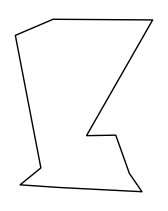

```mathematica
VertexSortFromLoopEdgeList[PartLoop4]
Graphics[Line2=Line[Pin[[%]]]]
```

```mathematica
ArcLength[Line2]//N
```

33.0305